```mathematica
Setup working directory and load API package
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<PlanetOS.m
<<PlanetOSconfigure.m
```

#### Request json data from Planet OS

```mathematica
jsondata = Stationdata["noaa_ndbc_stdmet_stations","62150",{count->100,"time_order"-> desc,"time_start"->"2015-09-18T18:00:00",offset->100}];
```

```mathematica
location={"longitude","latitude"}/.({"axes"}/.({"entries"}/.Flatten[jsondata]))//Flatten;
```

```mathematica
GeoListPlot[GeoPosition[location[[1;;2]]],GeoRange->{{-40., 50.}, {-30., 100.}}]
```

-Graphics-

#### Processing data and turn them into time-series data

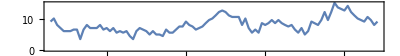

```mathematica
v=({"wind_spd"}/.({"data"}/.({"entries"}/.Flatten[jsondata]))//Flatten)/.{"wind_spd"->Missing["NotAvailable"]};
t={"time"}/.({"axes"}/.({"entries"}/.Flatten[jsondata]))//Flatten;
baddata[entry_]:=Not[MatchQ[entry,{_?NumberQ,__}]];
{v,t} = DeleteCases[{v,t}ᵀ,_?baddata]ᵀ;
windspeedts = TimeSeries[v,{t},MissingDataMethod->Automatic];
DateListPlot[windspeedts,AspectRatio->1/7,ImageSize->Full]
```

#### Create a simple cut-in cut-off wind turbine model

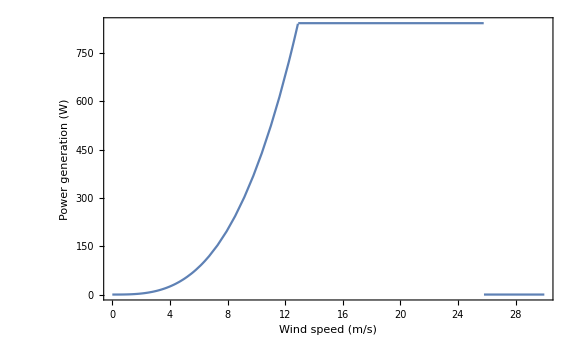

```mathematica
powerGeneration[v_, vRated_:Quantile[windspeedts, 0.95], A_:Pi/4] := 
   Piecewise[{{0, v <= 0}, {(v^3*A)/2, 0 <= v <= vRated}, {(vRated^3*A)/2, vRated <= v <= 2*vRated}, {0, v >= 2*vRated}}]; 
Plot[powerGeneration[v],{v,0,30} ,Frame->True,FrameLabel->{"Wind speed (m/s)","Power generation (W)"},ImageSize->Large,AspectRatio->1./GoldenRatio]
```

#### Evaluate wind power production and plot in time-series

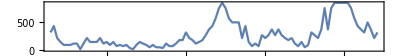

```mathematica
windpowerts = TimeSeriesMap[powerGeneration,windspeedts];
DateListPlot[windpowerts,AspectRatio->1/7,ImageSize->Full]
```

#### Mean power production at given period

```mathematica
Mean[windpowerts]
```

274.508